## Machine Learning II - Non-linear and Unsupervised

Jesse Galef - jesseg@wolfram.com

## Non-linear models:

### Nearest Neighbors: “What was the most common class of the training examples close?”

```mathematica
iris=Normal@RandomSample@ResourceData["Sample Data: Fisher's Irises"];
```

```mathematica
{iristrain,iristest}=TakeDrop[iris,120];
```

```mathematica
iristrain[[1]]
```

```mathematica
x=KeyDrop[iristrain,"Species"];
y=iristrain[[All,"Species"]];
```

```mathematica
newflower=iristest[[1]]
```

```mathematica
testdistances=DistanceMatrix[KeyDrop[iristest,"Species"], x];
```

```mathematica
testdistances[[1]];
```

```mathematica
y[[Ordering[testdistances[[1]]]]];
```

```mathematica
irisclassifier=Classify[iristrain->"Species", Method->"NearestNeighbors"]
```

```mathematica
Information[irisclassifier]
```

```mathematica
ClassifierMeasurements[irisclassifier, iristest]
```

## Decision Trees: “Guess Who”

```mathematica
SeedRandom[0];
wine=RandomSample[ResourceData["Sample Data: Wine Quality"]];
highquality=Normal[ReplaceAll[wine[[All,"WineQuality"]], {3|4|5|6->"Low", 7|8|9->"High"}]];
x=Normal[wine];
x[[All,"WineQuality"]]=highquality;
{train,test}=TakeDrop[x,3000];
```

```mathematica
Counts[train[[All,"WineQuality"]]]
Counts[train[[All,"WineQuality"]]]/3000//N
```

<|Low→2360,High→640|>

<|Low→0.786667,High→0.213333|>

```mathematica
train[[1]]
```

<|WineQuality→Low,FixedAcidity→5.7,VolatileAcidity→0.22,CitricAcid→0.22,ResidualSugar→16.65,Chlorides→0.044,FreeSulfurDioxide→39.,TotalSulfurDioxide→110.,Density→0.99855,PH→3.24,Sulphates→0.48,Alcohol→9.|>

```mathematica
features=DeleteCases[Keys[x[[1]]], "WineQuality"];
```

```mathematica
logisticmodel=Classify[train->"WineQuality",Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[logisticmodel, test[[All]]];
```

### Exploring splits

```mathematica
splitoptions=<|#->KeySort@PositionIndex[train[[All,#]]]&/@features|>;
```

```mathematica
Manipulate[
x=Keys[splitoptions[feature]][[splitposition]];
groupBars=GroupBy[train,#[feature]<=x&];
(*groupBars=KeySortBy[groupBars, True>False];*)
groupBars=Counts[#[[All,"WineQuality"]]]&/@groupBars;
groupBars=Lookup[#,{"High","Low"}]&/@groupBars;

Row[
{Labeled[Show[{Histogram[#[[All,feature]]&/@KeySort[GroupBy[train,#["WineQuality"]&]], 50,"Probability", 
ImageSize->500, ChartLegends->{"High","Low"}]
,
Graphics[{Thick,HalfLine[{x,0},{0,1}]}]
}],feature<>"<="<>ToString[x]<>"?"],
BarChart[{groupBars[True],groupBars[False]}, ImageSize->400,
PlotLabel->{"Left Group", "Right Group"}]
}]
,
{feature, features},{splitposition,1,Length[Keys[splitoptions[feature]]],1}];
```

```mathematica
%33
```

Lookup::invrl: The argument {631,2285} is not a valid Association or a list of rules.

Lookup::invrl: The argument {9,75} is not a valid Association or a list of rules.

### Building a Decision Tree

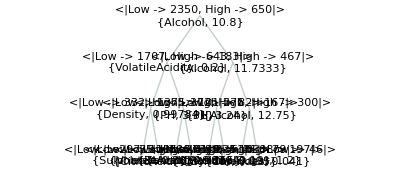
## 

### Automating a Decision Tree Builder

```mathematica
giniImpurity[data_List]:=giniImpurity[Counts[data]];
giniImpurity[counts_Association]:=Module[
{p},
p=Values[counts]/Total[counts];
1-Total[p^2]
];
splitImpurity[leftside_List, rightside_List]:=splitImpurity[Counts[leftside], Counts[rightside]];
splitImpurity[leftcounts_Association, rightcounts_Association]:=Module[
{impurities, weights},
weights=Total/@{leftcounts,rightcounts};
impurities=giniImpurity[#]&/@{leftcounts,rightcounts};
weights=weights/Total[weights];
Total[impurities*weights]
];
```

```mathematica
bestSplitOnFeature[data_, feature_] := Module[
   {possiblesplits, leftcounts, rightcounts, changingcounts, qualities},
   (* Keep a running tally of the survival counts in each split
   as we "move" blocks of elements to the left *)
   If[
    Length[Counts[data[[All, feature]]]] <= 1,
    (* If the values are all identical, we can't split *)
    <|"Feature" -> feature, "Impurity" -> Infinity|>
    ,
        (* Make an association of each value (e.g. class) and the list of which examples have that value
    <|1->{indices of examples in 1st class}, 2->{indices of examples in 2nd class} etc|> *)
    possiblesplits = KeySort[PositionIndex[data[[All, feature]]]];
    
    (* Track how many High/low in left/right as we move the dividing line right, trying each value as the SplitValue and measuring impurity *)
    rightcounts = Counts[data[[All, "WineQuality"]]];
    leftcounts = <|"Low" -> 0, "High" -> 0|>;
    qualities = <|KeyValueMap[#1 ->
         (changingcounts = Counts[data[[#2, "WineQuality"]]];
          leftcounts["Low"] = leftcounts["Low"] + Lookup[changingcounts, "Low", 0];
          rightcounts["Low"] = rightcounts["Low"] - Lookup[changingcounts, "Low", 0];
          leftcounts["High"] = leftcounts["High"] + Lookup[changingcounts, "High", 0];
          rightcounts["High"] = rightcounts["High"] - Lookup[changingcounts, "High", 0];
          splitImpurity[leftcounts, rightcounts]
          ) &
       , Most@possiblesplits]|>;
    <|"Feature" -> feature, "SplitValue" -> First[Keys[TakeSmallest[qualities, 1]]], "Impurity" -> N@Min[qualities]|>
    ]
   ];
```

```mathematica
Column[SortBy[bestSplitOnFeature[test,#]&/@features, "Impurity"]]
```

<|Feature→Alcohol,SplitValue→10.8,Impurity→0.301353|>
<|Feature→Chlorides,SplitValue→0.039,Impurity→0.321864|>
<|Feature→CitricAcid,SplitValue→0.23,Impurity→0.340067|>
<|Feature→Density,SplitValue→0.9926,Impurity→0.311097|>
<|Feature→FixedAcidity,SplitValue→7.4,Impurity→0.340578|>
<|Feature→FreeSulfurDioxide,SplitValue→46.,Impurity→0.34037|>
<|Feature→PH,SplitValue→3.27,Impurity→0.338619|>
<|Feature→ResidualSugar,SplitValue→6.9,Impurity→0.336898|>
<|Feature→Sulphates,SplitValue→0.67,Impurity→0.341607|>
<|Feature→TotalSulfurDioxide,SplitValue→153.,Impurity→0.333357|>
<|Feature→VolatileAcidity,SplitValue→0.19,Impurity→0.340793|>

```mathematica
buildTree[data_]:=buildTree[data,Infinity];
buildTree[data_, depth_]:=Module[
{possiblesplits,best,split,splitdata,outcomes},
outcomes=Counts[data[[All,"WineQuality"]]];
If[Or[depth<=0,Length[data]<=1,Length[outcomes]==1],outcomes, (*If there are too few points or only 1 outcome (e.g.all High),don't split*) 
possiblesplits=bestSplitOnFeature[data,#]&/@features;
split=First[TakeSmallestBy[possiblesplits,#[["Impurity"]]&,1]];
split["Status"]=outcomes;
If[split["Impurity"]==Infinity,outcomes,
splitdata=GroupBy[data,(#[split["Feature"]]<=split["SplitValue"])&];
Tree[KeyDrop[split,"Impurity"],
{buildTree[splitdata[True],depth-1],buildTree[splitdata[False], depth-1]}
]
]
]
];
```

```mathematica
tree=buildTree[train];//AbsoluteTiming
```

{5.28535,Null}

```mathematica
tree;
```

```mathematica
parseNode[node_]:=ToString[node["Status"]]<>"\n"<>ToString[Lookup[node,{"Feature","SplitValue"}]];
```

```mathematica
treeToDepth[tree_, n_]:=If[n<=0,
parseNode[TreeData[tree]],
Tree[parseNode[TreeData[tree]],treeToDepth[#,n-1]&/@TreeChildren[tree]]];
```

```mathematica
treeToDepth[tree,3]
```

-Graphics-

```mathematica
useTree[tree_,example_]:=useTree[tree,example, Infinity];
useTree[tree_, example_, depth_]:=Module[
{info, children},
info=TreeData[tree];
If[!KeyExistsQ[info,"Feature"],
First[Keys[TakeLargest[info,1]]] (* If this is a leaf with just the Outcomes *)
,
children=TreeChildren[tree];
If[depth<=0,
First[Keys[TakeLargest[info["Status"],1]]]
,
If[example[info["Feature"]]≤info["SplitValue"],
useTree[children[[1]],example, depth-1],
useTree[children[[2]],example, depth-1]
]
]
]
];
```

```mathematica
useTree[tree,train[[1]]]
```

Low

```mathematica
testTree[tree_, data_]:=testTree[tree,data,Infinity];
testTree[tree_, data_, depth_]:=Module[
{predictions,matrix, precision, recall},
predictions=useTree[tree,#, depth]&/@data;
matrix=Counts[Transpose[{predictions,data[[All,"WineQuality"]]}]]
];
```

```mathematica
accuracy[confusionmatrix_]:=N[Total[Lookup[confusionmatrix,{{"High","High"}, {"Low","Low"}},0]] / Total[confusionmatrix]];
```

```mathematica
accuracy[testTree[tree,train]]
```

1.

```mathematica
testTree[tree,test]
```

<|{High,Low}→178,{High,High}→249,{Low,Low}→1300,{Low,High}→171|>

```mathematica
ClassifierMeasurements[predictions, test[[All,"WineQuality"]]]
```

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of predictions.

ClassifierMeasurements[predictions,{Low,High,High,Low,Low,Low,High,High,Low,Low,High,Low,Low,High,High,Low,Low,High,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,High,High,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,High,Low,Low,Low,High,High,Low,Low,Low,Low,High,Low,High,High,High,Low,Low,Low,High,Low,Low,Low,Low,Low,High,High,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,High,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,High,Low,High,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,High,Low,Low,High,Low,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,High,High,Low,Low,Low,High,Low,High,Low,Low,Low,Low,High,High,Low,Low,High,High,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,High,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,High,High,Low,Low,Low,Low,High,Low,Low,High,Low,Low,High,Low,Low,High,High,Low,Low,High,High,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,High,Low,High,Low,High,Low,Low,High,Low,Low,High,Low,High,Low,Low,High,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,High,High,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,High,High,High,High,Low,Low,High,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,High,Low,High,Low,High,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,High,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,High,Low,High,Low,High,Low,High,Low,Low,High,Low,Low,Low,High,High,High,Low,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,High,High,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,High,High,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,High,Low,Low,High,Low,High,Low,Low,Low,Low,Low,High,Low,Low,High,Low,High,Low,Low,High,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,High,Low,Low,High,Low,Low,High,High,High,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,High,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,High,Low,Low,High,Low,High,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,High,High,High,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,High,Low,High,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,High,Low,High,Low,Low,High,Low,Low,High,High,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,High,High,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,High,High,Low,High,Low,Low,Low,Low,Low,High,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,High,High,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,High,High,Low,High,High,High,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,High,Low,Low,Low,Low,Low,High,Low,High,Low,High,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,High,High,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,High,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,High,High,Low,High,High,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,High,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,High,Low,High,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,High,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,High,High,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,High,Low,Low,High,Low,Low,Low,High,Low,High,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,Low,Low,High,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,High,Low,Low,Low,High,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,High,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,High,High,Low,Low,Low,Low,High,High,High,Low,Low,Low,Low,High,High,Low,Low,Low,Low,Low,Low,High,High,Low,High,High,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,High,Low,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,High,High,Low,High,Low,High,High,Low,Low,High,Low,High,Low,High,High,High,High,Low,Low,Low,Low,High,Low,High,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,Low,High,Low,Low,High,High,Low,Low,High,Low,Low,Low,Low,Low,Low,High,High,High,Low,Low,High,Low,Low,Low,High}]

## Improvements?

```mathematica
forest=Table[buildTree[RandomChoice[train,1000]],25];
```

RandomChoice::lrwl: The items for choice train should be a non-empty list or a rule weights -> choices.

```mathematica
useForest[example_]:=Commonest[useTree[#,example]&/@forest,1]
```

```mathematica
predictions=useForest/@test[[;;1000]];
```

```mathematica
predictions=Flatten[predictions];
Count[Transpose[{predictions,test[[;;1000,"WineQuality"]]}],{x_,x_}]/1000//N
```

```mathematica
ClassifierMeasurements[predictions, test[[;;1000,"WineQuality"]]]
```

## Unsupervised Learning

## Clustering

```mathematica
SeedRandom[42];
data=RandomReal[1,{100,3}];
rotator=IdentityMatrix[{3,3}]+{0,.75,.75};
colors=RGBColor@@@Dot[data,rotator]
```

```mathematica
FindClusters[colors]
```

## Problem 1: Scale matters

```mathematica
ListPlot[Flatten[CoordinateBoundsArray[{{0,10},{0,25}},{1,1}],1], Axes->False];
ListPlot[Flatten[CoordinateBoundsArray[{{0,10},{0,25}},{1,12}],1],Axes->False];
```

```mathematica
x=;
```

## Problem 2: What the heck do we even want?

```mathematica
ListPlot[x]
```

## Different Algorithms Give Different Clusters:

### K-Means: Iteratively move cluster centers

```mathematica
kMeansCluster[data_, k_]:=kMeansCluster[data,k,RandomSample[data,k]];
kMeansCluster[data_, k_, centers_]:=Module[
{distances, assignments, newcenters},
distances=DistanceMatrix[data,centers];
assignments=PositionIndex[Sow[Ordering[#,1]&/@distances]];
newcenters=centers;
KeyValueMap[(newcenters[[First[#1]]]=Mean[data[[#2]]])&,assignments];
Sow[newcenters,"centers"];
If[newcenters!=centers,newcenters= kMeansCluster[data,k,newcenters]];
newcenters
];
```

```mathematica
{centers,{assignments, centerpath}}=Reap[kMeansCluster[x,5]];
```

```mathematica
colors={Red,Blue,Black,Green,Gray};
```

```mathematica
groupedpoints=Table[MapThread[Style[#1,colors[[#2]]]& ,{x,assignments[[step]]}],{step,Length[assignments]}];
```

```mathematica
Manipulate[
Show[{ListPlot[groupedpoints[[step]], PlotStyle->PointSize[0.01]],
ListPlot[centerpath[[step]],PlotStyle->{Orange,PointSize[0.05]}]}],
{step,1,Length[assignments],1}];
```

### DBScan

"DBSCAN" defines "core points" as data points that have more than k neighbors within a ball of ϵ radius (i . e . data points in high - density regions) . Then, core points that are at a distance of less than ϵ from each other define a cluster . Furthermore, any point that is at a distance of less than ϵ of a core point belongs to the cluster of the core point . Any point that is not near a core point is considered noise .

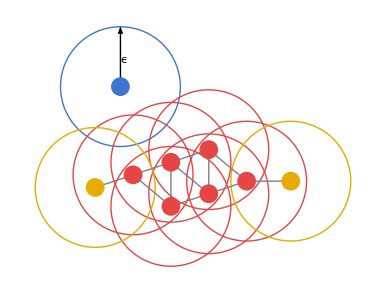

```mathematica
ListPlot[FindClusters[x, Method->"DBSCAN"], PlotStyle->PointSize[0.01]]
```

### Agglomerate: Iteratively join nearest clusters together

```mathematica
ListPlot[FindClusters[x,UpTo[10], Method->"Agglomerate"], PlotStyle->PointSize[0.01]]
```

### Spectral, JarvisPatrick, Spanning Tree...

## Dimensionality reduction

```mathematica
Graphics3D[Style[Cuboid[List@@#,List@@#+{.075,.075,.075}],#]&/@colors]
```

```mathematica
colorreducer=DimensionReduction[colors,1];
```

```mathematica
ListPlot[Style[Append[colorreducer[#],0],#]&/@colors, Axes->False,PlotStyle->Directive[PointSize->Large], Background->Blue]
```

```mathematica
SeedRandom[0];
wine=RandomSample[ResourceData["Sample Data: Wine Quality"]];
highquality=Normal[ReplaceAll[wine[[All,"WineQuality"]], {3|4|5|6->"Low", 7|8|9->"High"}]];
x=Normal[wine];
x[[All,"WineQuality"]]=highquality;
{train,test}=TakeDrop[x,3000];
```

```mathematica
reduced=DimensionReduce[KeyDrop[train,"WineQuality"],3];//AbsoluteTiming
```

```mathematica
ListPointPlot3D[{Pick[reduced,#WineQuality=="High"&/@train],Pick[reduced,#WineQuality=="Low"&/@train]}, PlotRange->Automatic]
```

```mathematica
SeedRandom[12]
data=Table[Insert[AngleVector[1+{2,8}*RandomReal[]],RandomReal[],2],1000];
ListPointPlot3D[data,BoxRatios->{1,1,1},PlotStyle->Directive[PointSize->Large]]
```

```mathematica
reducer=DimensionReduction[data,2,Method->"Isomap"]
```

```mathematica
reducedpts=reducer[data];
ListPlot[Style[#,Hue[First[#]/20]]&/@reducedpts,AspectRatio->1/2,PlotStyle->Directive[PointSize->Small]]
```

```mathematica
ListPointPlot3D[Style[#,Hue[First[reducer[#]]/20]]&/@data,PlotStyle->Directive[PointSize->Large],BoxRatios->{1,1,1}]
```

```mathematica
pca=DimensionReduction[data,Method->"PrincipalComponentsAnalysis"];
```

```mathematica
ListPlot[Map[Style[pca[#],Hue[First[reducer[#]]/20]]&, data]]
```